```mathematica
<<Notation`
```

```mathematica
Notation[x[[n_]] ⟺ Subscript[x, n_]]
```

```mathematica
(* All the numerical coefficients are defined at the beginning *)
a=1.;
m=1.;
ℏ=0.1;
```

```mathematica
n=20;
ξ=Range[-π/(2a),π/(2a),n];(* The interval of n k-values sampled along the interval *)
```

```mathematica
2 t Cos[]
```

Cos::argx: Cos called with 0 arguments; 1 argument is expected.

2 t Cos[]

```mathematica
Array[(ℏ Norm[#]^2)/(2m)+# δ&,{
```

25

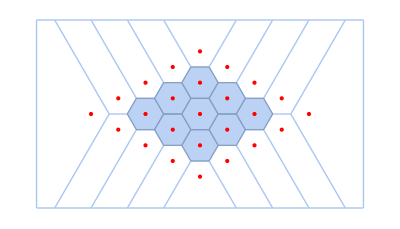

```mathematica
β=N@{a{(√3)/2,1/2},a{(√3)/2,-1/2}}; 
G=Tuples[Range[-2,2],2].β; 
Length@G (* Number of sampled points *)
(* 1BZ represented for a honeycomb lattice *)
Show[VoronoiMesh[G,PlotTheme->"Lines",MeshCellStyle->{{2,"Interior"}->Directive[Opacity[0.8]]}],Graphics[{Red,Point[G]}],PlotRange->Automatic]
```

61

9

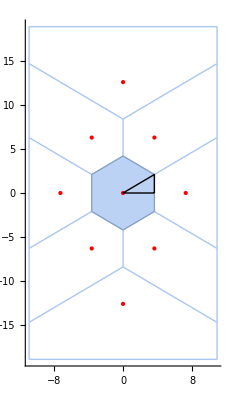

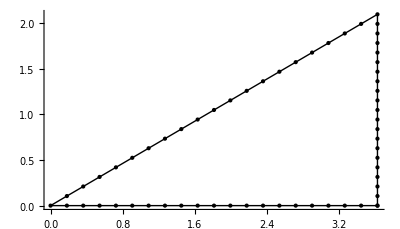

```mathematica
bas=N@{(2π)/(a √3){1,√3},(2π)/(a √3){1,-√3}}; 
path=N@With[{Γ={0,0},K={2/3,1/3}.bas,M={1/2,1/2}.bas},{M,Γ,K,M}]; (* The list of high-symmetry points *)
samplPts=Subdivide[#1,#2,n]&@@@Partition[path,2,1]//Flatten[#,1]&//DeleteAdjacentDuplicates;(* List of n points sampled along each line of the path going through the high-symmetry points, it's literally the points generated by traversing the line, although not in equal steps *)
Length@samplPts (* Total count of the sampling points *)
K=Tuples[Range[-1,1],2].bas; 
Length@K (* Number of sampled points *)
Show[VoronoiMesh[K,PlotTheme->"Lines",MeshCellStyle->{{2,"Interior"}->Directive[Opacity[0.8]]}],Graphics[{{Red,Point[K]},{Thick,Line[path]}}],PlotRange->Automatic,Axes->True]
Graphics[{Point[#]&/@samplPts,Line[path]},Axes->True]
```

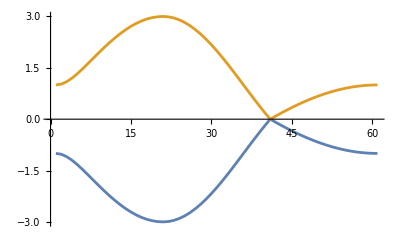

```mathematica
t=1.;
fnband=t √(3+2Cos[a #2]+4Cos[(√3)/2 a #1]Cos[a/2#2])&@@@samplPts;
pm[a_]:={-a,a};
ListLinePlot[±fnband,PlotRange->Automatic]
```